## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="SHK3Dr";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_SHK3Dr_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3dhsk,Null;nadph,Null;,Keq substrate}

{1.1×10^14,Keq value}

{3dhsk,Null;nadph,Null;,Keq substrate}

{1.1×10^12,Keq value}

{skm,Km or S05 substrate}

{2.9×10^-6,Km or S05 value}

{{{skm,Null}},kcat substrates}

{0.091,kcat value}

{nadp,Km or S05 substrate}

{0.000056,Km or S05 value}

{{{nadp,Null}},kcat substrates}

{237.,kcat value}

{skm,Km or S05 substrate}

{0.000065,Km or S05 value}

{{{skm,Null}},kcat substrates}

{237.,kcat value}

{nadp,Km or S05 substrate}

{0.0001,Km or S05 value}

{{{nadp,Null}},kcat substrates}

{0.117,kcat value}

{skm,Km or S05 substrate}

{0.00012,Km or S05 value}

{{{skm,Null}},kcat substrates}

{0.117,kcat value}

((3dhsk)^c+nadph^c⇌nadp^c+skm^c)^SHK3Dr

ordered Bi Bi;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3dhsk,Null;nadph,Null; | 1.1×10^14 | 1.045×10^14
1.155×10^14 | Null | Null | 7 | Null | Null | Null
1 | 3dhsk,Null;nadph,Null; | 1.1×10^12 | 1.045×10^12
1.155×10^12 | Null | Null | 9 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | skm | 2.9×10^-6 | 2.8×10^-6
3.×10^-6 |  | M | 9 | 20 |  | 
1 | nadp | 0.000056 | 0.0000532
0.0000588 |  | M | 9 | 20 |  | 
1 | skm | 0.000065 | 0.00006175
0.00006825 |  | M | 9 | 20 |  | 
1 | nadp | 0.0001 | 0.000095
0.000105 |  | M | 9 | 20 |  | 
1 | skm | 0.00012 | 0.000114
0.000126 |  | M | 9 | 20 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | skm | Null | 0.091 | 0.09
0.092 | 1/s | 9 | 20 |  | 
1 | nadp | Null | 237. | 225.15
248.85 | 1/s | 9 | 20 |  | 
1 | skm | Null | 237. | 225.15
248.85 | 1/s | 9 | 20 |  | 
1 | nadp | Null | 0.117 | 0.11115
0.12285 | 1/s | 9 | 20 |  | 
1 | skm | Null | 0.117 | 0.11115
0.12285 | 1/s | 9 | 20 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {0,1};
kmPriorities = {1,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1,1,1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3dhsk)^c+nadph^c⇌nadp^c+skm^c)^SHK3Dr

ordered Bi Bi;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3dhsk,Null;nadph,Null; | 1.1×10^12 | 1.045×10^12
1.155×10^12 | Null | Null | 9 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | skm | 2.9×10^-6 | 2.8×10^-6
3.×10^-6 |  | M | 9 | 20 |  | 
1 | nadp | 0.000056 | 0.0000532
0.0000588 |  | M | 9 | 20 |  | 
1 | skm | 0.000065 | 0.00006175
0.00006825 |  | M | 9 | 20 |  | 
1 | nadp | 0.0001 | 0.000095
0.000105 |  | M | 9 | 20 |  | 
1 | skm | 0.00012 | 0.000114
0.000126 |  | M | 9 | 20 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | skm | Null | 0.091 | 0.09
0.092 | 1/s | 9 | 20 |  | 
1 | nadp | Null | 237. | 225.15
248.85 | 1/s | 9 | 20 |  | 
1 | skm | Null | 237. | 225.15
248.85 | 1/s | 9 | 20 |  | 
1 | nadp | Null | 0.117 | 0.11115
0.12285 | 1/s | 9 | 20 |  | 
1 | skm | Null | 0.117 | 0.11115
0.12285 | 1/s | 9 | 20 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_SHK3Dr[c] + nadph[c] <=> E_SHK3Dr[c]&nadph",
				"E_SHK3Dr[c]&nadph + 3dhsk[c] <=> E_SHK3Dr[c]&nadph&3dhsk",
				"E_SHK3Dr[c]&nadph&3dhsk <=> E_SHK3Dr[c]&nadp&skm",
				"E_SHK3Dr[c]&nadp&skm <=> E_SHK3Dr[c]&nadp + skm[c]",
                                            "E_SHK3Dr[c]&nadp <=> E_SHK3Dr[c] + nadp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((SHK3Dr^c)_^+nadph^c⇌(SHK3Dr^c&nadph^c)_^)^SHK3Dr1,((SHK3Dr^c&nadp^c)_^⇌(SHK3Dr^c)_^+nadp^c)^SHK3Dr2,((SHK3Dr^c&nadph^c)_^+(3dhsk)^c⇌(SHK3Dr^c&nadph^c&(3dhsk)^c)_^)^SHK3Dr3,((SHK3Dr^c&nadp^c&skm^c)_^⇌(SHK3Dr^c&nadp^c)_^+skm^c)^SHK3Dr4,((SHK3Dr^c&nadph^c&(3dhsk)^c)_^⇌(SHK3Dr^c&nadp^c&skm^c)_^)^SHK3Dr5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((SHK3Dr^c)_^+nadph^c⇌(SHK3Dr^c&nadph^c)_^)^SHK3Dr1,Overscript[(SHK3Dr^c&nadp^c)_^⇌(SHK3Dr^c)_^+nadp^c, SHK3Dr2],((SHK3Dr^c&nadph^c)_^+(3dhsk)^c⇌(SHK3Dr^c&nadph^c&(3dhsk)^c)_^)^SHK3Dr3,Overscript[(SHK3Dr^c&nadp^c&skm^c)_^⇌(SHK3Dr^c&nadp^c)_^+skm^c, SHK3Dr4],((SHK3Dr^c&nadph^c&(3dhsk)^c)_^⇌(SHK3Dr^c&nadp^c&skm^c)_^)^SHK3Dr5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3dhsk)^c→0,nadph^c→0}

{nadp^c→0,skm^c→0}

{(3dhsk)^c→∞,nadph^c→∞}

{nadp^c→∞,skm^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((SHK3Dr^c&nadph^c&(3dhsk)^c)_^-((SHK3Dr^c&nadp^c&skm^c)_^)/K_SHK3Dr5) Volume_c k_SHK3Dr5^⟶}

Volume_c (-(SHK3Dr^c&nadp^c&skm^c)_^ k_SHK3Dr5^⟵+(SHK3Dr^c&nadph^c&(3dhsk)^c)_^ k_SHK3Dr5^⟶)

1

2

3

0.385736

4

0.000923

5

0.00015

Simplifying...

6

0.17081

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
Print[relativeRateForward]
```

{((3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr2^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+nadph^c k_SHK3Dr1^⟶ (k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵+k_SHK3Dr5^⟶))))/((3dhsk)^c k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr1^⟵ k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)+nadph^c k_SHK3Dr1^⟶ ((3dhsk)^c k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ ((3dhsk)^c k_SHK3Dr3^⟶+k_SHK3Dr5^⟶)+(3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr5^⟵+k_SHK3Dr5^⟶)))),(nadph^c k_SHK3Dr1^⟶ ((3dhsk)^c k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+(3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵+k_SHK3Dr5^⟶))))/((3dhsk)^c k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr1^⟵ k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)+nadph^c k_SHK3Dr1^⟶ ((3dhsk)^c k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+(3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵+k_SHK3Dr5^⟶))))}

```mathematica
FilePrint@dataPathList
```

Priority	3dhsk[c]	nadp[c]	nadph[c]	skm[c]	param_SHK3Dr_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt"	1.1e12
1	0	0.01	0	2.900000000000003e-7	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.09090909090909098
1	0	0.01	0	4.596190258137236e-7	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.13680688860321016
1	0	0.01	0	7.284470651377796e-7	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.20076000891310203
1	0	0.01	0	1.1545107946051446e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.28474724895080183
1	0	0.01	0	1.8297762989925615e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.3868631798468571
1	0	0.01	0	2.9000000000000027e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.5000000000000002
1	0	0.01	0	4.596190258137236e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.6131368201531433
1	0	0.01	0	7.284470651377796e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7152527510491989
1	0	0.01	0	0.000011545107946051446	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7992399910868986
1	0	0.01	0	0.000018297762989925615	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.86319311139679
1	0	0.01	0	0.00002900000000000003	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.9090909090909092
1	0	5.600000000000003e-6	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.09090909090909095
1	0	8.875401877782245e-6	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.13680688860321014
1	0	0.00001406656401645367	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.200760008913102
1	0	0.00002229400155099584	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.28474724895080133
1	0	0.000035333611290890826	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.38686317984685703
1	0	0.00005600000000000003	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.5000000000000001
1	0	0.00008875401877782245	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.6131368201531433
1	0	0.0001406656401645367	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.7152527510491988
1	0	0.00022294001550995864	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.7992399910868984
1	0	0.0003533361129089083	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.86319311139679
1	0	0.0005600000000000004	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.9090909090909093
1	0	0.01	0	6.500000000000002e-6	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.09090909090909094
1	0	0.01	0	0.000010301805750997245	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.13680688860321008
1	0	0.01	0	0.000016327261804812287	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.20076000891310192
1	0	0.01	0	0.000025876966085977307	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.28474724895080133
1	0	0.01	0	0.000041012227391212555	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.386863179846857
1	0	0.01	0	0.00006500000000000002	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.5000000000000001
1	0	0.01	0	0.00010301805750997245	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.6131368201531432
1	0	0.01	0	0.00016327261804812288	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7152527510491987
1	0	0.01	0	0.0002587696608597733	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7992399910868984
1	0	0.01	0	0.0004101222739121255	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.8631931113967899
1	0	0.01	0	0.0006500000000000002	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.9090909090909092
1	0	0.00001	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.09090909090909091
1	0	0.00001584893192461114	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.13680688860321005
1	0	0.000025118864315095822	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.20076000891310186
1	0	0.000039810717055349695	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.2847472489508013
1	0	0.00006309573444801929	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.3868631798468568
1	0	0.0001	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.5
1	0	0.00015848931924611142	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.6131368201531432
1	0	0.0002511886431509582	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.7152527510491988
1	0	0.00039810717055349735	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.7992399910868982
1	0	0.000630957344480193	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.8631931113967899
1	0	0.001	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt"	0.9090909090909091
1	0	0.01	0	0.000012000000000000007	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.09090909090909095
1	0	0.01	0	0.00001901871830953338	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.13680688860321014
1	0	0.01	0	0.000030142637178115006	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.20076000891310197
1	0	0.01	0	0.00004777286046641966	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.28474724895080133
1	0	0.01	0	0.0000757148813376232	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.386863179846857
1	0	0.01	0	0.00012000000000000008	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.5000000000000002
1	0	0.01	0	0.00019018718309533382	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.6131368201531432
1	0	0.01	0	0.00030142637178115007	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7152527510491989
1	0	0.01	0	0.0004777286046641971	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.7992399910868982
1	0	0.01	0	0.0007571488133762321	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.86319311139679
1	0	0.01	0	0.0012000000000000008	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt"	0.9090909090909091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.091
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	237.
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117
1	0	0.01	0	0.01	1	9	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt"	0.117

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateFor_3dhsk.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateFor_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateFor_3dhsk.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateFor_nadph.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_nadp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/relRateRev_skm.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 165.026124532
best_fit: 164.917601163
best_fit: 165.073547629
best_fit: 165.082035607
best_fit: 164.873633129

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/SHK3Dr.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | haldaneRatio_1 | 0.607196 | 0.368687 | 8.28233×10^11 | 75.2939 | 1.1×10^12 | 2.71767×10^11
1 | relRateRev_skm | 1.19414 | 1.42597 | 0.0850952 | 93.6047 | 0.0909091 | 0.00581392
1 | relRateRev_skm | 1.17311 | 1.37619 | 0.127624 | 93.2875 | 0.136807 | 0.00918322
1 | relRateRev_skm | 1.14201 | 1.30418 | 0.186283 | 92.7891 | 0.20076 | 0.0144767
1 | relRateRev_skm | 1.09745 | 1.2044 | 0.261996 | 92.01 | 0.284747 | 0.0227513
1 | relRateRev_skm | 1.03629 | 1.0739 | 0.351278 | 90.8017 | 0.386863 | 0.0355849
1 | relRateRev_skm | 0.956651 | 0.915181 | 0.444752 | 88.9503 | 0.5 | 0.0552483
1 | relRateRev_skm | 0.85905 | 0.737967 | 0.528315 | 86.1659 | 0.613137 | 0.0848218
1 | relRateRev_skm | 0.746981 | 0.557981 | 0.587174 | 82.0932 | 0.715253 | 0.128079
1 | relRateRev_skm | 0.626572 | 0.392592 | 0.610395 | 76.3719 | 0.79924 | 0.188845
1 | relRateRev_skm | 0.505503 | 0.255533 | 0.593665 | 68.7754 | 0.863193 | 0.269529
1 | relRateRev_skm | 0.391578 | 0.153333 | 0.540088 | 59.4097 | 0.909091 | 0.369002
1 | relRateRev_nadp | 0.05037 | 0.00253713 | 0.0111795 | 12.2975 | 0.0909091 | 0.102089
1 | relRateRev_nadp | 0.0476819 | 0.00227356 | 0.0158758 | 11.6046 | 0.136807 | 0.152683
1 | relRateRev_nadp | 0.0439639 | 0.00193283 | 0.0213873 | 10.6532 | 0.20076 | 0.222147
1 | relRateRev_nadp | 0.0391291 | 0.00153109 | 0.0268464 | 9.42817 | 0.284747 | 0.311594
1 | relRateRev_nadp | 0.0333223 | 0.00111038 | 0.0308515 | 7.97477 | 0.386863 | 0.417715
1 | relRateRev_nadp | 0.0269781 | 0.00072782 | 0.0320447 | 6.40895 | 0.5 | 0.532045
1 | relRateRev_nadp | 0.0207253 | 0.00042954 | 0.0299694 | 4.88789 | 0.613137 | 0.643106
1 | relRateRev_nadp | 0.0151579 | 0.000229762 | 0.0254048 | 3.55186 | 0.715253 | 0.740658
1 | relRateRev_nadp | 0.0106318 | 0.000113034 | 0.0198073 | 2.47826 | 0.79924 | 0.819047
1 | relRateRev_nadp | 0.00721662 | 0.0000520797 | 0.0144634 | 1.67557 | 0.863193 | 0.877657
1 | relRateRev_nadp | 0.0047821 | 0.0000228685 | 0.0100655 | 1.1072 | 0.909091 | 0.919156
1 | relRateRev_skm | 0.105419 | 0.0111131 | 0.0249755 | 27.4731 | 0.0909091 | 0.115885
1 | relRateRev_skm | 0.0994361 | 0.00988753 | 0.0351993 | 25.7292 | 0.136807 | 0.172006
1 | relRateRev_skm | 0.0912352 | 0.00832387 | 0.0469323 | 23.3773 | 0.20076 | 0.247692
1 | relRateRev_skm | 0.0806954 | 0.00651175 | 0.0581428 | 20.4191 | 0.284747 | 0.34289
1 | relRateRev_skm | 0.0682158 | 0.0046534 | 0.065798 | 17.0081 | 0.386863 | 0.452661
1 | relRateRev_skm | 0.0547956 | 0.00300256 | 0.0672384 | 13.4477 | 0.5 | 0.567238
1 | relRateRev_skm | 0.0417777 | 0.00174538 | 0.0619119 | 10.0976 | 0.613137 | 0.675049
1 | relRateRev_skm | 0.0303539 | 0.000921358 | 0.0517791 | 7.23928 | 0.715253 | 0.767032
1 | relRateRev_skm | 0.0211782 | 0.000448517 | 0.0399406 | 4.99732 | 0.79924 | 0.839181
1 | relRateRev_skm | 0.014319 | 0.000205035 | 0.0289346 | 3.35204 | 0.863193 | 0.892128
1 | relRateRev_skm | 0.00946228 | 0.0000895348 | 0.0200244 | 2.20268 | 0.909091 | 0.929115
1 | relRateRev_nadp | 0.268673 | 0.0721851 | 0.077855 | 85.6405 | 0.0909091 | 0.168764
1 | relRateRev_nadp | 0.250289 | 0.0626448 | 0.106636 | 77.9465 | 0.136807 | 0.243443
1 | relRateRev_nadp | 0.225906 | 0.0510337 | 0.136981 | 68.2312 | 0.20076 | 0.337741
1 | relRateRev_nadp | 0.195833 | 0.0383507 | 0.162238 | 56.976 | 0.284747 | 0.446985
1 | relRateRev_nadp | 0.161869 | 0.0262017 | 0.174736 | 45.1675 | 0.386863 | 0.5616
1 | relRateRev_nadp | 0.127103 | 0.0161552 | 0.169997 | 33.9995 | 0.5 | 0.669997
1 | relRateRev_nadp | 0.0949149 | 0.00900884 | 0.149771 | 24.4271 | 0.613137 | 0.762908
1 | relRateRev_nadp | 0.0677784 | 0.00459392 | 0.120808 | 16.8903 | 0.715253 | 0.836061
1 | relRateRev_nadp | 0.0466642 | 0.00217755 | 0.0906604 | 11.3433 | 0.79924 | 0.8899
1 | relRateRev_nadp | 0.031248 | 0.000976435 | 0.0643966 | 7.46028 | 0.863193 | 0.92759
1 | relRateRev_nadp | 0.0205119 | 0.000420739 | 0.0439669 | 4.83636 | 0.909091 | 0.953058
1 | relRateRev_skm | 0.331062 | 0.109602 | 0.103927 | 114.32 | 0.0909091 | 0.194836
1 | relRateRev_skm | 0.306692 | 0.0940602 | 0.140398 | 102.625 | 0.136807 | 0.277204
1 | relRateRev_skm | 0.274866 | 0.0755516 | 0.177285 | 88.307 | 0.20076 | 0.378045
1 | relRateRev_skm | 0.236327 | 0.0558505 | 0.20592 | 72.3166 | 0.284747 | 0.490667
1 | relRateRev_skm | 0.193655 | 0.0375022 | 0.217381 | 56.1906 | 0.386863 | 0.604244
1 | relRateRev_skm | 0.15081 | 0.0227438 | 0.207588 | 41.5176 | 0.5 | 0.707588
1 | relRateRev_skm | 0.111816 | 0.0125027 | 0.180045 | 29.3646 | 0.613137 | 0.793182
1 | relRateRev_skm | 0.079394 | 0.00630341 | 0.143471 | 20.0588 | 0.715253 | 0.858724
1 | relRateRev_skm | 0.0544307 | 0.0029627 | 0.106718 | 13.3524 | 0.79924 | 0.905958
1 | relRateRev_skm | 0.0363402 | 0.00132061 | 0.0753369 | 8.7277 | 0.863193 | 0.93853
1 | relRateRev_skm | 0.0238063 | 0.00056674 | 0.0512239 | 5.63463 | 0.909091 | 0.960315
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 1.16619 | 1.36001 | 1.24324 | 1366.2 | 0.091 | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 2.24951 | 5.06031 | 235.666 | 99.437 | 237. | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424
1 | absRateRev | 1.05705 | 1.11735 | 1.21724 | 1040.38 | 0.117 | 1.33424

### Simulated Data and Best Fit Data Plot

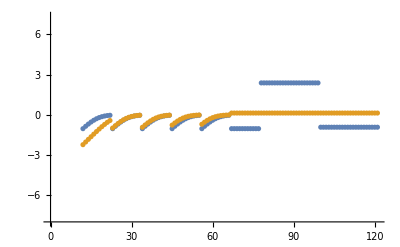

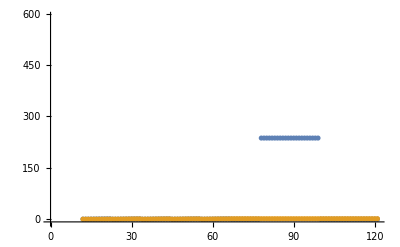

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

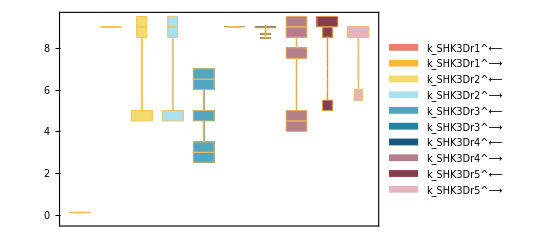

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

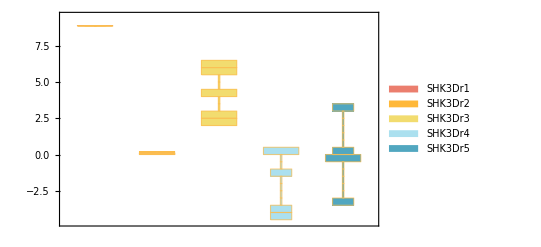

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24]
(*Histogram*)
```

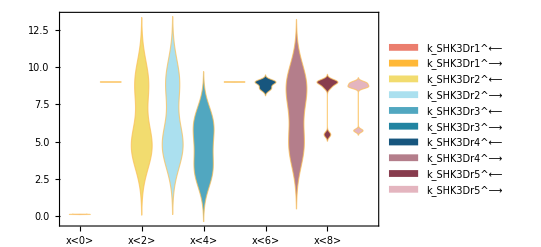

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

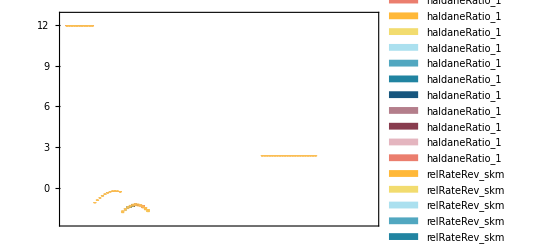

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
2.9×10^-6 | 0.0000495903 | 1610.01
0.000056 | 0.0000492543 | 12.0459
0.000065 | 0.0000495903 | 23.7073
0.0001 | 0.0000492543 | 50.7457
0.00012 | 0.0000495903 | 58.6748

```mathematica
Print[absoluteRateForward]
```

((3dhsk)^c nadph^c SHK3Dr_total_Global k_SHK3Dr1^⟶ k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)/((3dhsk)^c k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr1^⟵ k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)+nadph^c k_SHK3Dr1^⟶ ((3dhsk)^c k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+(3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵+k_SHK3Dr5^⟶))))

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.091 | (3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c) | 1098.9 Abs[0.091-(3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c)]
237. | (3.42882×10^31 skm^c)/(1.34086 (9.39332×10^26+3.84848×10^24 skm^c)+6.64465×10^6 (1.29436×10^18+3.84849×10^24 skm^c)) | 0.421941 Abs[237.-(3.42882×10^31 skm^c)/(1.34086 (9.39332×10^26+3.84848×10^24 skm^c)+6.64465×10^6 (1.29436×10^18+3.84849×10^24 skm^c))]
237. | (3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c) | 0.421941 Abs[237.-(3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c)]
0.117 | (3.42882×10^31 skm^c)/(1.34086 (9.39332×10^26+3.84848×10^24 skm^c)+6.64465×10^6 (1.29436×10^18+3.84849×10^24 skm^c)) | 854.701 Abs[0.117-(3.42882×10^31 skm^c)/(1.34086 (9.39332×10^26+3.84848×10^24 skm^c)+6.64465×10^6 (1.29436×10^18+3.84849×10^24 skm^c))]
0.117 | (3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c) | 854.701 Abs[0.117-(3.42882×10^31 nadp^c)/(1.25956×10^27+2.55727×10^31 nadp^c)]

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 3.82622×10^-9